# Symmetry test

## Initialization and options

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];
```

```mathematica
Middle[l_List]:=Part[l,Floor[Length[l]/2]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};

(* Opciones de los procedimientos *)
windowsize = 1000;
resolution = 40;
symmetryPoints = 50;
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Load database

```mathematica
database = Import[FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}]];
AddToDataset[database,"TrendReturns",TrendReturns,{"Prices"}];
AddToDataset[database,"DatedTrendReturns",DatedTrendReturns,{"Dates","Prices"}];
AddToDataset[database,"VelocityTrendReturns",VelocityTrendReturns,{"Prices"}];
AddToDataset[database,"DatedVelocityTrendReturns",DatedVelocityTrendReturns,{"Dates","Prices"}];
orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
```

## Extreme event detection

```mathematica
extremeDates = ProgressMap[GetExtremeEventDates[#["DatedTrendReturns"]]&,database];
```

```mathematica
importantDates = FindImportantDates[extremeDates,3]
```

{Day: Fri 7 Sep 2001,Day: Wed 1 Oct 2008}

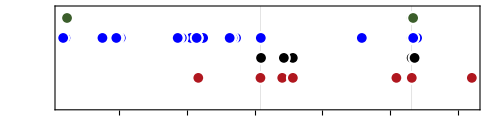

```mathematica
TimelinePlot[extremeDates,
PlotLegends->database[[All,"Name"]],
GridLines->{importantDates,None},
PlotTheme->"Monochrome",
PlotStyle->colors,
FrameLabel->{Style["Date",bigFontSize]}, 
ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
PlotMarkers->None,
Frame->True
]
```

```mathematica
importantDates = {DateObject[{2001,9,7},"Day","Gregorian",-5.],DateObject[{2008,10,1},"Day","Gregorian",-5.]};
```

```mathematica
importantDatesNames = {"DotCom Crisis","2008 Crisis"};
```

## Crisis interval

```mathematica
dotCom = {DateObject[{2000,3,10}],DateObject[{2002,10,9}]}
```

{Day: Fri 10 Mar 2000,Day: Wed 9 Oct 2002}

```mathematica
bigFuckup = {DateObject[{2007,8,9}],DateObject[{2009,4,2}]}
```

{Day: Thu 9 Aug 2007,Day: Thu 2 Apr 2009}

```mathematica
importantIntervals = {dotCom,bigFuckup}
```

{{Day: Fri 10 Mar 2000,Day: Wed 9 Oct 2002},{Day: Thu 9 Aug 2007,Day: Thu 2 Apr 2009}}

Add database information

```mathematica
rules = {"DotCom Crisis"-> "(a)","2008 Crisis"->"(b)","Brexit"->"(c)","Tequila effect"->"(d)","Japanese asset\nprice bubble"->"(e)"};
```

```mathematica
AddKeyToMarket[database[[1]],"ImportantDates"->{DateObject[{2001,9,7},"Day","Gregorian",-5.],DateObject[{2008,10,1},"Day","Gregorian",-5.],DateObject[{2016,6,23},"Day","Gregorian",-5.]}];
AddKeyToMarket[database[[1]],"ImportantIntervals"->{{DateObject[{2000,3,10},"Day","Gregorian",-5.],DateObject[{2002,10,9},"Day","Gregorian",-5.]},{DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2009,4,2},"Day","Gregorian",-5.]},{DateObject[{2016,6,23},"Day","Gregorian",-5.],Today}}];
AddKeyToMarket[database[[1]],"ImportantDatesNames"->{"DotCom Crisis","2008 Crisis","Brexit"}/.rules];

AddKeyToMarket[database[[2]],"ImportantDates"->{DateObject[{2001,9,7},"Day","Gregorian",-5.],DateObject[{2008,10,1},"Day","Gregorian",-5.]}];
AddKeyToMarket[database[[2]],"ImportantIntervals"->{{DateObject[{2000,3,10},"Day","Gregorian",-5.],DateObject[{2002,10,9},"Day","Gregorian",-5.]},{DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2009,4,2},"Day","Gregorian",-5.]}}];
AddKeyToMarket[database[[2]],"ImportantDatesNames"->{"DotCom Crisis","2008 Crisis"}/.rules];

AddKeyToMarket[database[[3]],"ImportantDates"->{DateObject[{1994,12,7},"Day","Gregorian",-6.],DateObject[{2008,10,1},"Day","Gregorian",-5.]}];
AddKeyToMarket[database[[3]],"ImportantIntervals"->{{DateObject[{1994,1,1},"Day","Gregorian",-5.],DateObject[{2001,1,1},"Day","Gregorian",-5.]},{DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2009,4,2},"Day","Gregorian",-5.]}}];
AddKeyToMarket[database[[3]],"ImportantDatesNames"->{"Tequila effect","2008 Crisis"}/.rules];

AddKeyToMarket[database[[4]],"ImportantDates"->{DateObject[{1992,8,17},"Day","Gregorian",-6.],DateObject[{2008,10,1},"Day","Gregorian",-5.]}];
AddKeyToMarket[database[[4]],"ImportantIntervals"->{{DateObject[{1990,1,1},"Day","Gregorian",-5.],DateObject[{1993,1,1},"Day","Gregorian",-5.]},{DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2009,4,2},"Day","Gregorian",-5.]}}];
AddKeyToMarket[database[[4]],"ImportantDatesNames"->{"Japanese asset\nprice bubble","2008 Crisis"}/.rules];
```

## Returns distribution

```mathematica
MakeStatisticTable[marketnames_,dists_] := Module[{gridmm},
gridmm = {Join[{""},marketnames],
Join[{"μ"},Table[Mean[i],{i,dists}]],
Join[{"σ"}, Table[StandardDeviation[i],{i,dists}]],
Join[{"Skewness"}, Table[Skewness[i],{i,dists}]],
Join[{"Kurtosis"}, Table[Kurtosis[i],{i,dists}]]};
Grid[gridmm,
Alignment->Left,
Spacings->{2,1},
Frame->All,
ItemStyle->"Text",
Background->{{LightGray,None},{Gray,None}}
]
];
```

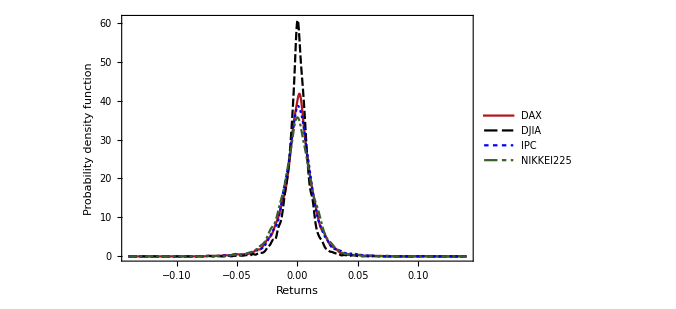

```mathematica
SmoothHistogram[database[[All,"Returns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["Returns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"Returns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000319714 | 0.000296114 | 0.000555369 | -0.0000312847
σ | 0.0142415 | 0.0107171 | 0.0148833 | 0.0151916
Skewness | -0.106661 | -0.176113 | 0.0226418 | -0.203261
Kurtosis | 7.30022 | 11.569 | 9.35525 | 8.09446

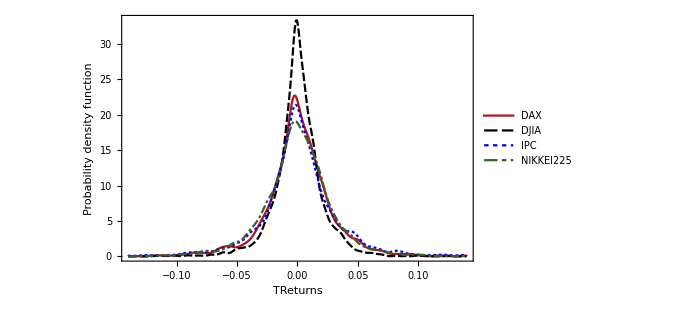

```mathematica
SmoothHistogram[database[[All,"TrendReturns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["TReturns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"TrendReturns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000631323 | 0.000563473 | 0.00120697 | -0.000059991
σ | 0.0295203 | 0.0208431 | 0.0342922 | 0.0300463
Skewness | -0.729049 | -0.693697 | -0.241625 | -0.569394
Kurtosis | 10.8335 | 14.9535 | 9.67833 | 11.9555

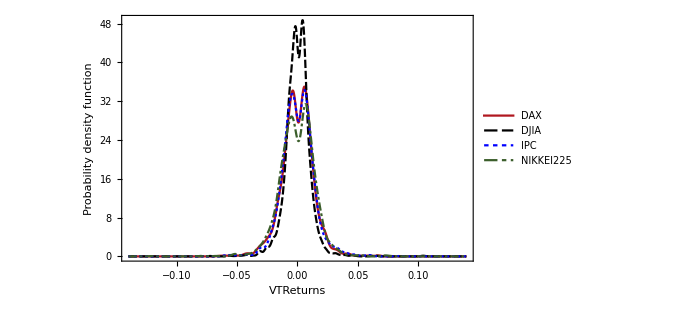

```mathematica
SmoothHistogram[database[[All,"VelocityTrendReturns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["VTReturns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"VelocityTrendReturns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000127415 | 0.000166781 | 0.00046062 | -0.0000621582
σ | 0.0131252 | 0.0103054 | 0.0131251 | 0.0142704
Skewness | -0.0275892 | 0.378788 | 0.152915 | -0.257632
Kurtosis | 5.43131 | 13.9691 | 5.84517 | 6.8131

```mathematica
hr = Map[{#["Name"],MeasureHeightRatio[#["VelocityTrendReturns"]]}&,database];
```

```mathematica
Grid[Prepend[hr,{"Name","Height ratio"}],Frame->All,Background->{None,{LightGray}}]
```

Name | Height ratio
DAX | 1.0235
DJIA | 1.02463
IPC | 1.02328
NIKKEI225 | 1.08783

## Distribution decomposition by runs

```mathematica
DayLegends[n_]:=Map[
If[# == 1,
StringJoin[ToString[#]," day"],
StringJoin[ToString[#]," days"]
]
&,
Range[n]
];

GroupReturnsByRun[market_,returnType_]:=KeySort[GroupBy[Thread[{TrendDuration[market["Prices"]],market[returnType]}],First->Last]];
PlotTrendDistributionByRuns[market_,returnType_]:=Block[{grouped},
grouped = Select[GroupReturnsByRun[market,returnType],Length[#]>40&];
SmoothHistogram[Take[grouped,4],
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style[returnType/.{"TrendReturns"->"TReturns","VelocityTrendReturns"->"TVReturns"},bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[4],{Left,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotLabel->market["Name"]
]
];
```

Trend Returns

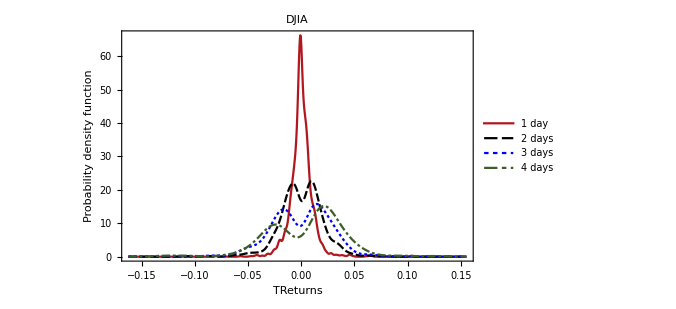
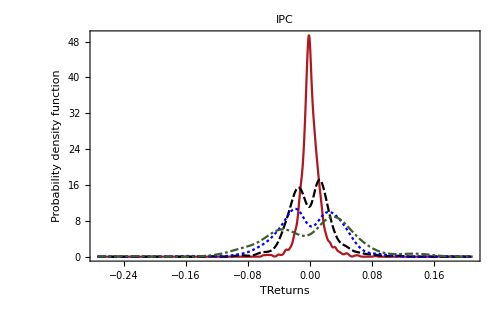
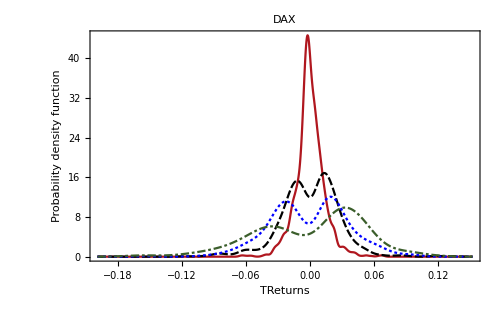
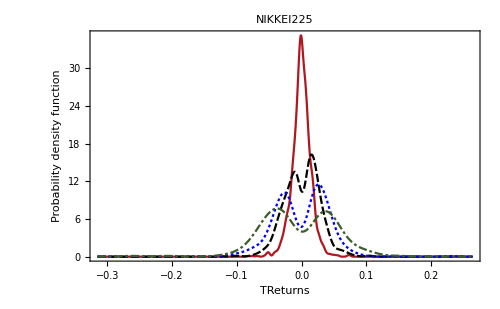

```mathematica
Map[PlotTrendDistributionByRuns[#,"TrendReturns"]&,orderedDatabase]
```

Velocity Trend Returns

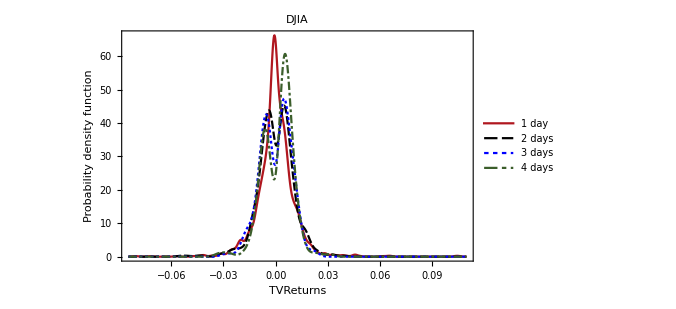
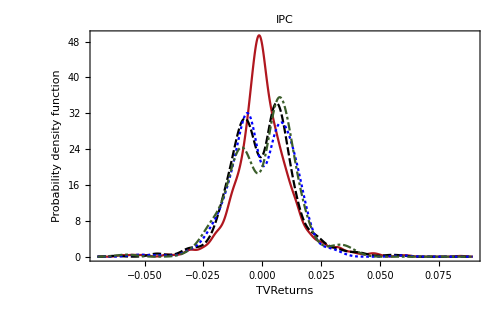
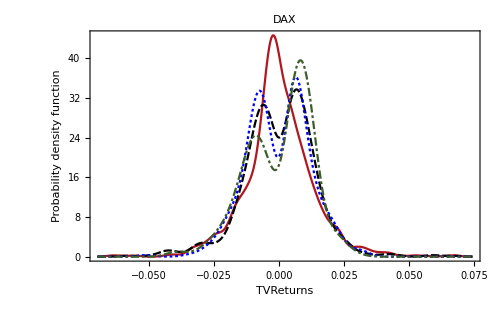
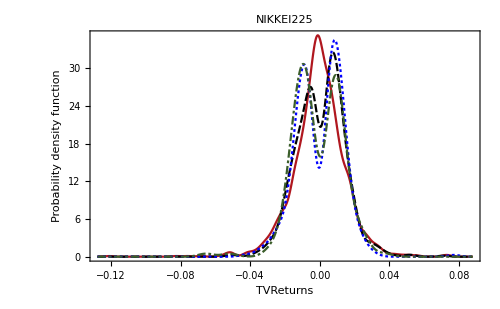

```mathematica
Map[PlotTrendDistributionByRuns[#,"VelocityTrendReturns"]&,orderedDatabase]
```

## Symmetry analysis

```mathematica
UpperPercentagePointLine[cmin_,cmax_,cl_]:= {{cmin, UpperPercentagePoint[cl]},{cmax,UpperPercentagePoint[cl]}};

PlotSymmetry[market_,returnType_]:= Module[{returns,standardError,tn,upperLineLimit,meanline,cMax,cMin,cFill,cline,upp,plotData,p},
returns = market[returnType];
standardError = StandardDeviation[returns] / Sqrt[Length[returns]];
tn = MeasureTn[returns];
upperLineLimit = Max[tn["TnValues"][[All,2]]];

(* Plot lines *)
meanline=Line[{{Mean[returns],0},{Mean[returns],upperLineLimit/2.5}}];

cMin = Line[{{tn["PlausibleSymmMin"],0},{tn["PlausibleSymmMin"],upperLineLimit/2.5}}];
cMax = Line[{{tn["PlausibleSymmMax"],0},{tn["PlausibleSymmMax"],upperLineLimit/2.5}}];
cFill = Rectangle[{tn["PlausibleSymmMin"],0},{tn["PlausibleSymmMax"],upperLineLimit/2.5}];

cline = Line[{{MinimalBy[tn["TnValues"],Last][[1,1]],0},{MinimalBy[tn["TnValues"],Last][[1,1]],upperLineLimit/2.5}}];
upp = Map[UpperPercentagePointLine[tn["MinimumC"],tn["MaximumC"],#]&,{0.01,0.05,0.1}];
plotData = Join[{tn["TnValues"]},upp];

p = ListLinePlot[plotData,
PlotTheme->"Monochrome",
FrameLabel->{
Style["c",bigFontSize],
Style["T_n(c)",bigFontSize]
},
Epilog->{
meanline,
cline,
cMin,
cMax,

{
Gray,
Opacity[0.4],
cFill
},

Inset[Text["μ"],{Mean[returns],upperLineLimit/2}],
Inset[Text["C_Max"],{tn["PlausibleSymmMax"],upperLineLimit/2}],
Inset[Text["C_Min"],{tn["PlausibleSymmMin"],upperLineLimit/2}],
Inset[Text["C"],{MinimalBy[tn["TnValues"],Last][[1,1]],1.7+upperLineLimit/2}]
},
PlotLegends->If[market["Name"]=="DJIA",Placed[{"T_n","99% CL","95% CL","90% CL"},{Right,Top}],None], 
PlotLabel->market["Name"],ImageSize->plotSize,Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,PlotMarkers->None, PlotStyle->colors
];
Return[p];
];
```

Returns

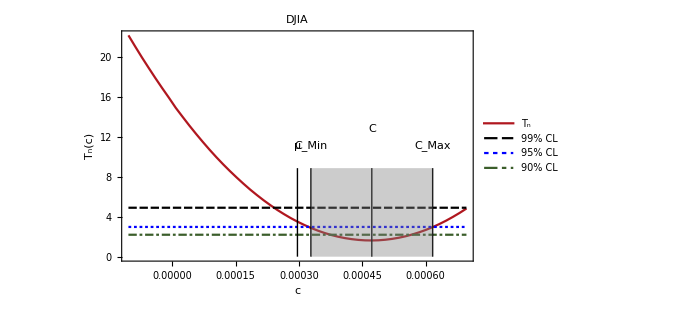
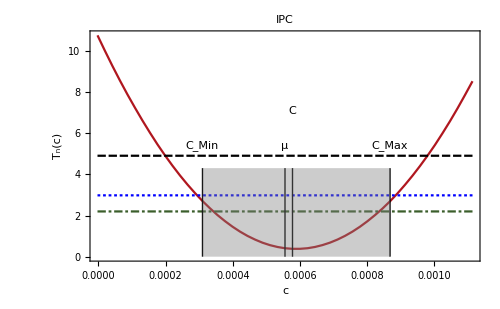
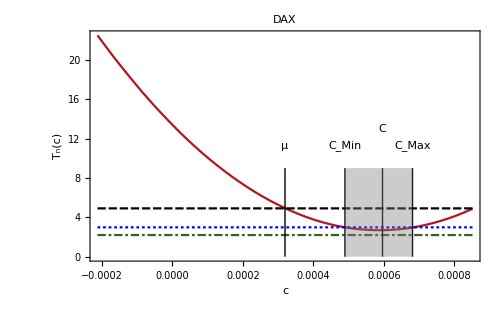
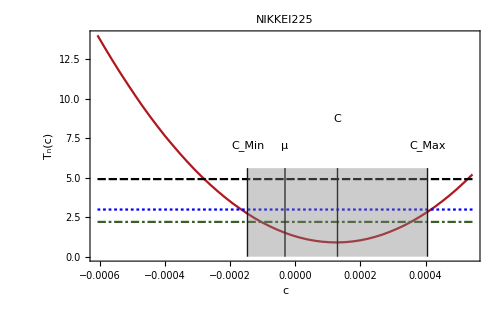

```mathematica
ProgressMap[PlotSymmetry[#,"Returns"]&,orderedDatabase]
```

Trend returns

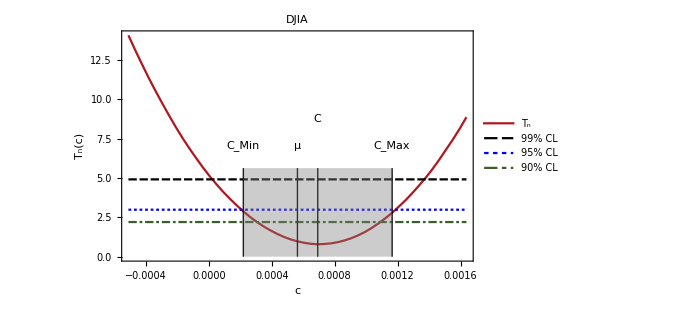
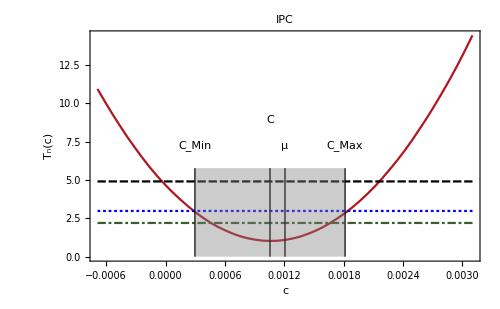
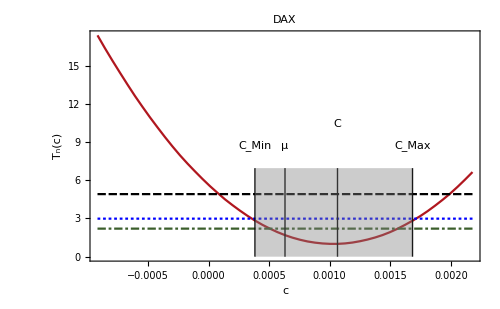
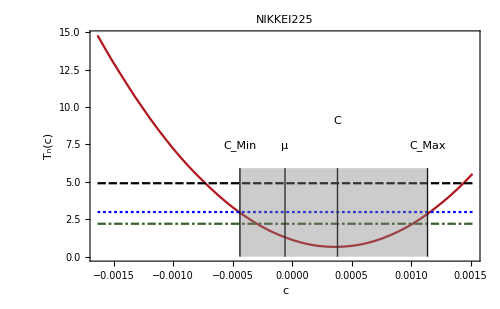

```mathematica
Map[PlotSymmetry[#,"TrendReturns"]&,orderedDatabase]
```

Velocity trend returns

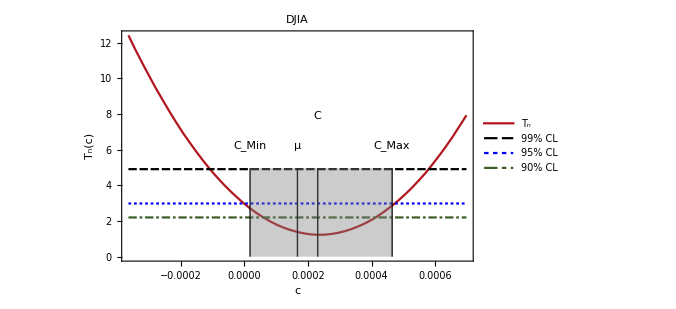
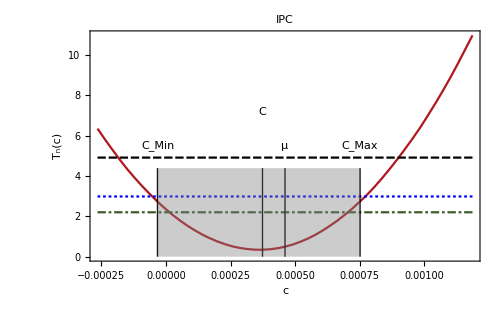
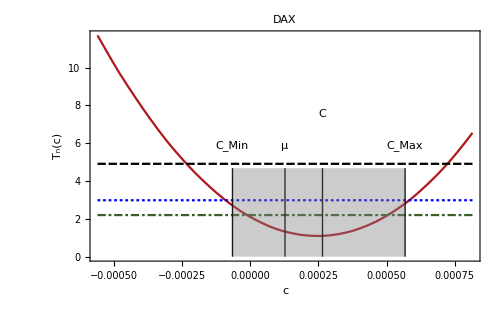
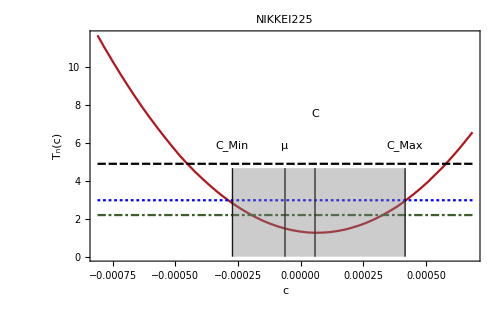

```mathematica
Map[PlotSymmetry[#,"VelocityTrendReturns"]&,orderedDatabase]
```

## Symmetry tables of the test when c=0

```mathematica
ReportSymmetry[market_,returnType_,cl_]:= Block[{data, returns},
returns =  market[returnType];
If[Tn[N[returns],0.0] ≤ UpperPercentagePoint[cl],
Return[Item["Symmetric",Background->RGBColor[0.2,1,0.2]]],
Return[Item["Asymmetric",Background->RGBColor[1,0.2,0.2]]]
];
];
MarketSymmetryReport[market_,cl_]:= Join[
{market["Name"]},
Table[ReportSymmetry[market,returnType,cl],{returnType,{"Returns","TrendReturns","VelocityTrendReturns"}}]
];
MakeSymmetryTable[database_,cl_]:=Block[{symmTable,grid},
symmTable = Table[MarketSymmetryReport[market,cl],{market,database}];

grid = Grid[
Join[
{
{"CL = "<>ToString[cl],SpanFromLeft,SpanFromLeft},
{Style["Market",Bold],Style["R",Bold],Style["R_T",Bold],Style["VR_T",Bold]}
}
,
symmTable
]
,
Frame->All,
Background->{{LightGray},{Gray}}
];
Return[grid];
];
```

```mathematica
Table[MakeSymmetryTable[database,cl],{cl,{0.01,0.05,0.1}}]
```

{CL = 0.01 |  |  | 
Market | R | R_T | VR_T
DAX | Asymmetric | Asymmetric | Symmetric
DJIA | Asymmetric | Asymmetric | Symmetric
IPC | Asymmetric | Symmetric | Symmetric
NIKKEI225 | Symmetric | Symmetric | Symmetric,CL = 0.05 |  |  | 
Market | R | R_T | VR_T
DAX | Asymmetric | Asymmetric | Symmetric
DJIA | Asymmetric | Asymmetric | Symmetric
IPC | Asymmetric | Asymmetric | Symmetric
NIKKEI225 | Symmetric | Symmetric | Symmetric,CL = 0.1 |  |  | 
Market | R | R_T | VR_T
DAX | Asymmetric | Asymmetric | Symmetric
DJIA | Asymmetric | Asymmetric | Asymmetric
IPC | Asymmetric | Asymmetric | Asymmetric
NIKKEI225 | Symmetric | Symmetric | Symmetric}

```mathematica
MarketRowTn[market_,returnType_]:=Block[{tn},
tn = MeasureTn[market[returnType],0.05,350];
{
market["Name"],
returnType,
ToString[tn["Mean"]],StringJoin["(",TextString[tn["PlausibleSymmMin"]],", ",ToString[tn["PlausibleSymmMax"]],")"],
ToString[tn["BestSymmetry"]],
If[tn["Tn(0)"]<UpperPercentagePoint[0.05],"Yes","No"]
}
];
```

```mathematica
orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
marketTables = ProgressMap[Table[MarketRowTn[#,returnType],{returnType,{"Returns","TrendReturns","VelocityTrendReturns"}}]&,orderedDatabase];
```

```mathematica
Grid[
Join[{{"Market","Observable","μ","Symmetry Interval","C","Zero Symmetric"}},Concatenate[marketTables]],
Background->{None,{LightBlue}},
Frame->All
]
```

Market | Observable | μ | Symmetry Interval | C | Zero Symmetric
DJIA | Returns | 0.000296114 | (0.000323572, 0.000616454) | 0.000470013 | No
DJIA | TrendReturns | 0.000563473 | (0.000207432, 0.00118348) | 0.000692385 | No
DJIA | VelocityTrendReturns | 0.000166781 | (-0.000000150935, 0.000470294) | 0.000230519 | Yes
IPC | Returns | 0.000555369 | (0.000294031, 0.000883634) | 0.000590426 | No
IPC | TrendReturns | 0.00120697 | (0.000286817, 0.00183484) | 0.00107707 | No
IPC | VelocityTrendReturns | 0.00046062 | (-0.0000531519, 0.000767226) | 0.00036118 | Yes
DAX | Returns | 0.000319714 | (0.000489751, 0.000681043) | 0.000589952 | No
DAX | TrendReturns | 0.000631323 | (0.000365994, 0.00171033) | 0.00103816 | No
DAX | VelocityTrendReturns | 0.000127415 | (-0.0000888628, 0.000583565) | 0.000249317 | Yes
NIKKEI225 | Returns | -0.0000312847 | (-0.000162716, 0.000415581) | 0.000129718 | Yes
NIKKEI225 | TrendReturns | -0.000059991 | (-0.000437956, 0.0011549) | 0.00036297 | Yes
NIKKEI225 | VelocityTrendReturns | -0.0000621582 | (-0.000284413, 0.000416544) | 0.0000617915 | Yes

## Descriptive statistics

```mathematica
MarketRowStat[market_,returnType_]:=Block[{rets},
rets = market[returnType];

{
market["Name"],
returnType,
ToString[Length[rets]],
ToString[Count[rets,_?Positive]],
ToString[Count[rets,_?Negative]],
ToString[Count[rets,x_/;x==0]],
ToString[Mean[rets]],
ToString[StandardDeviation[rets]],
ToString[Skewness[rets]],
ToString[Kurtosis[rets]]
}
];
```

```mathematica
orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
```

```mathematica
marketTables = Map[Table[MarketRowStat[#,returnType],{returnType,{"Returns","TrendReturns","VelocityTrendReturns"}}]&,orderedDatabase];
```

```mathematica
Grid[
Join[{{"Market","Observable","Entries","Positive Events", "Negative events","Zero events","μ","σ","Skewness","Kurtosis"}},Concatenate[marketTables]],
Background->{None,{LightBlue}},
Frame->All
]
```

Market | Observable | Entries | Positive Events | Negative events | Zero events | μ | σ | Skewness | Kurtosis
DJIA | Returns | 6447 | 3391 | 3012 | 44 | 0.000296114 | 0.0107171 | -0.176113 | 11.569
DJIA | TrendReturns | 3388 | 1677 | 1670 | 41 | 0.000563473 | 0.0208431 | -0.693697 | 14.9535
DJIA | VelocityTrendReturns | 3388 | 1677 | 1670 | 41 | 0.000166781 | 0.0103054 | 0.378788 | 13.9691
IPC | Returns | 6409 | 3362 | 3041 | 6 | 0.000555369 | 0.0148833 | 0.0226418 | 9.35525
IPC | TrendReturns | 2949 | 1472 | 1471 | 6 | 0.00120697 | 0.0342922 | -0.241625 | 9.67833
IPC | VelocityTrendReturns | 2949 | 1472 | 1471 | 6 | 0.00046062 | 0.0131251 | 0.152915 | 5.84517
DAX | Returns | 6465 | 3457 | 3004 | 4 | 0.000319714 | 0.0142415 | -0.106661 | 7.30022
DAX | TrendReturns | 3274 | 1634 | 1636 | 4 | 0.000631323 | 0.0295203 | -0.729049 | 10.8335
DAX | VelocityTrendReturns | 3274 | 1634 | 1636 | 4 | 0.000127415 | 0.0131252 | -0.0275892 | 5.43131
NIKKEI225 | Returns | 6282 | 3183 | 3094 | 5 | -0.0000312847 | 0.0151916 | -0.203261 | 8.09446
NIKKEI225 | TrendReturns | 3276 | 1636 | 1635 | 5 | -0.000059991 | 0.0300463 | -0.569394 | 11.9555
NIKKEI225 | VelocityTrendReturns | 3276 | 1636 | 1635 | 5 | -0.0000621582 | 0.0142704 | -0.257632 | 6.8131

## Trend duration table

```mathematica
TDRowStat[market_]:=Block[{duration,trendLength,events},
duration = TrendDuration[market["Prices"]];
trendLength = Sort[DeleteDuplicates[duration]];
events = Map[Count[duration,#]&,Range[13]];
Join[{market["Name"]},events]
];

TDRowStatSigned[market_,signf_]:=Block[{duration,trendLength,events},
duration = Select[Thread[{TrendDuration[market["Prices"]],TrendReturns[market["Prices"]]}],signf[Last[#]]&][[All,1]];
trendLength = Sort[DeleteDuplicates[duration]];
events = Map[Count[duration,#]&,Range[13]];
Join[{market["Name"]},events]
];
```

```mathematica
m = Map[TDRowStatSigned[#,Positive]&,orderedDatabase]
```

{{DJIA,824,425,200,129,46,25,16,6,2,2,1,1,0},{IPC,629,372,204,119,67,40,18,12,6,5,0,0,0},{DAX,754,436,200,114,72,30,13,7,2,1,1,3,1},{NIKKEI225,821,429,211,89,41,23,12,5,4,0,0,1,0}}

```mathematica
Labeled[
Grid[
Join[{{"Market","1","2","3","4","5","6","7","8","9","10","11","12","13"}},Map[TDRowStatSigned[#,Negative]&,orderedDatabase]],
Background->{None,{LightBlue}},
Frame->All
],
Style["Negativos",Bold],
Top
]
```

Market | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
DJIA | 914 | 423 | 183 | 84 | 40 | 18 | 5 | 3 | 0 | 0 | 0 | 0 | 0
IPC | 698 | 369 | 209 | 90 | 56 | 24 | 14 | 4 | 6 | 1 | 0 | 0 | 0
DAX | 879 | 408 | 197 | 86 | 40 | 15 | 8 | 1 | 1 | 0 | 1 | 0 | 0
NIKKEI225 | 862 | 403 | 196 | 101 | 39 | 15 | 11 | 3 | 4 | 0 | 0 | 1 | 0Negativos